```mathematica
ExpPrint[exp_]:=Block[
{t=Table[exp[[k]],{k,1,Length[exp]}], cellformat},
cellformat=Framed[TextCell[#,CellSize->{550,Automatic}, TextAlignment->Left,FontSize->12]]&;
t=Map[cellformat,Sort[t,ExpComp]];
TableForm[t]
]
```

```mathematica
SameEdges[g_,h_]:=Block[{result=True},
If[EdgeCount[g]!=EdgeCount[h],Return[False]];
Table[If[!EdgeQ[g,e],result=False],{e,EdgeList[h]}];
result
]
```

```mathematica
SameVertices[g_,h_]:=Block[{result=True},
If[VertexCount[g]!=VertexCount[h],Return[False]];
Table[If[!VertexQ[g,v],result=False],{v,VertexList[h]}];
result
]
```

```mathematica
FindGraph5[g_]:=Block[{isomorph},
isomorph=Select[Keys[stubbornForm],
With[{h=stubbornForm[#,"graph"]},
IsomorphicGraphQ[g,h]&&
SameEdges[g,h]&&
SameVertices[g,h]
]&];
First[isomorph]
]
```

```mathematica
FindGraph5[CycleGraph[5]]
```

20665

```mathematica
AddEdge5[g_,code_,vertices_]:=Block[{h=g,decoded=PadLeft[IntegerDigits[code,2],3,0],i},
If[decoded[[1]]==1,h=EdgeAdd[h,vertices[[1]]<->vertices[[2]]]];
If[decoded[[2]]==1,h=EdgeAdd[h,vertices[[1]]<->vertices[[3]]]];
If[decoded[[3]]==1,h=EdgeAdd[h,vertices[[2]]<->vertices[[3]]]];
If[decoded[[3]]==1,h=EdgeAdd[h,vertices[[1]]<->vertices[[4]]]];
If[decoded[[3]]==1,h=EdgeAdd[h,vertices[[2]]<->vertices[[4]]]];
If[decoded[[3]]==1,h=EdgeAdd[h,vertices[[3]]<->vertices[[4]]]];
h
]
```

```mathematica
FindRelations5[g_,verticesg_,h_,verticesh_]:=Block[{g2,h2,keyg,keyh},
Table[
g2=AddEdge5[g,code,verticesg];
h2=AddEdge5[h,code,verticesh];
keyg=FindGraph5[g2];
keyh=FindGraph5[h2];
(*Print[Graph[g2,VertexLabels->"Name"],keyg,Graph[h2,VertexLabels->"Name"],keyh];*)
{keyg,keyh}
,{code,0,15}
]
]
```

```mathematica
FindRelations5[Graph[{1,2,3,4,5},{1<->2,1<->5}],{2,3,4,5},Graph[{1,2,3,4,5},{1<->2,1<->5}],{2,3,4,5}]
```

{{20412,20412},{20452,20452},{20493,20493},{20533,20533},{20655,20655},{20695,20695},{20736,20736},{20776,20776},{20412,20412},{20452,20452},{20493,20493},{20533,20533},{20655,20655},{20695,20695},{20736,20736},{20776,20776}}

```mathematica
ColorTablePrint[1,stubbornForm,"colofour3","colortable3"]
```

-Graphics-1b06Greater
( | = | ≠
1<->2 | b06-b25 | b25
1<->3 | b06-b16 | b16
1<->4 | 1/2 (-b03+b06+b10-b33) | 1/2 (b03+b06-b10+b33)
1<->5 | 1/2 (b03+b06-b10-b33) | 1/2 (-b03+b06+b10+b33)
2<->3 | b06-b22 | b22
2<->4 | 1/2 (b02-b05+b06-b26) | 1/2 (-b02+b05+b06+b26)
2<->5 | 1/2 (-b02+b05+b06-b26) | 1/2 (b02-b05+b06+b26)
3<->4 | 1/2 (b04+b06-b07-b34) | 1/2 (-b04+b06+b07+b34)
3<->5 | 1/2 (-b04+b06+b07-b34) | 1/2 (b04+b06-b07+b34)
4<->5 | 0 | b06)

```mathematica
repfive={b01->B01,b02->B02,b03->B03,b04->B04,b05->B05,b06->B06,b07->B07,b08->B08,b09->B09,b10->B10,b11->B11,b12->B12,b13->B13,b14->B14,b15->B15,b16->B16,b17->B17,b18->B18,b19->B19,b20->B20,s01->S01,s02->S02,s03->S03,s04->S04,s05->S05,s06->S06,s07->S07,s08->S08,s09->S09,s10->S10,s11->S11,s12->S12,s13->S13,s14->S14,s15->S15,s16->S16,s17->S17,s18->S18,s19->S19,s20->S20,z->Z,α->Α,α1->Α1,β->Β,β1->Β1,γ->Γ,γ1->Γ1,δ->Δ,δ1->Δ1,ϵ->Ε,ϵ1->Ε1,ζ->Ζ}
```

{b01→B01,b02→B02,b03→B03,b04→B04,b05→B05,b06→B06,b07→B07,b08→B08,b09→B09,b10→B10,b11→B11,b12→B12,b13→B13,b14→B14,b15→B15,b16→B16,b17→B17,b18→B18,b19→B19,b20→B20,s01→S01,s02→S02,s03→S03,s04→S04,s05→S05,s06→S06,s07→S07,s08→S08,s09→S09,s10→S10,s11→S11,s12→S12,s13→S13,s14→S14,s15→S15,s16→S16,s17→S17,s18→S18,s19→S19,s20→S20,z→Z,α→Α,α1→Α1,β→Β,β1→Β1,γ→Γ,γ1→Γ1,δ→Δ,δ1→Δ1,ϵ→Ε,ϵ1→Ε1,ζ→Ζ}

```mathematica
BeautyPrint[key_,assoc_:stubbornForm]:=Block[{current4=assoc[key], title, cellformat},
cellformat=TextCell[#,CellFrame->{{0,0},{0,.5}},CellFrameColor->Darker[Green],CellSize->{280,Automatic}, TextAlignment->Center,FontSize->11]&;
title=Style[key,If[ToString[assoc[key]["comp"]]=="Greater",Darker[Darker[Green]],Red],Bold];
Labeled[
Graph[current4["graph"]
 ,ImageSize->{50,50},VertexSize->.2,VertexStyle->Red],title,Top]
]
```

```mathematica
Compare5[xxx_,yyy_,colofour_:"colofour3",colortable_:"colortable4"]:=Block[
{current4=stubbornForm[xxx],current5=stubbornForm[yyy], result={}, table4,table5, title, title2,cellformat},
table4=current4[colortable];
table5=current5[colortable];
cellformat=TextCell[#,CellFrame->{{0,0},{0,.5}},CellFrameColor->Darker[Green],CellSize->{280,Automatic}, TextAlignment->Center,FontSize->11]&;
title="";cellformat[With[{t=ToString[stubbornForm[xxx]["comp"]]},Style[stubbornForm[xxx][colofour],If[t=="Greater",Darker[Darker[Green]],Red]]]];
title2="";cellformat[With[{t=ToString[stubbornForm[yyy]["comp"]]},Style[stubbornForm[yyy][colofour],If[t=="Greater",Darker[Darker[Green]],Red]]]];
(*Print[Labeled[
Graph[current4["graph"]
 ,ImageSize->{50,50},VertexSize->.2,VertexStyle->Red],{title,Style[xxx,Bold,Underlined]},{Bottom,Top}]
->Labeled[
Graph[current5["graph"],ImageSize->{50,50},VertexSize->.2,VertexStyle->Red],{title2,Style[yyy,Bold,Underlined]},{Bottom,Top}]];*)
(*Print[ColorTablePrint[xxx,stubbornForm,colofour,colortable]];*)

Table[
AppendTo[result,(table4[[ind,1]])==(table5[[ind,1]]/.repfive)];
AppendTo[result,(table4[[ind,2]])==(table5[[ind,2]]/.repfive)];,
{ind,Range[5,10]}
];
(*Print[ExpPrint[Fold[And,DeleteDuplicates[result]]]];*)
result
]
```

```mathematica
Compare5[20412,20412];
```

```mathematica
rels5=FindRelations5[Graph[{1,2,3,4,5},{1<->2,1<->5}],{2,3,4,5},Graph[{1,2,3,4,5},{1<->2,1<->5}],{4,5,2,3}]
```

{{20412,20412},{20452,20694},{20493,20493},{20533,20775},{20655,20413},{20695,20695},{20736,20494},{20776,20776},{20412,20412},{20452,20694},{20493,20493},{20533,20775},{20655,20413},{20695,20695},{20736,20494},{20776,20776}}

```mathematica
eqs5=Flatten[Map[Compare5[#[[1]],#[[2]]]&,rels5]];
```

```mathematica
ExpressionToTableLoc[exp_]:=Block[
{vals=Sort[Monitor[Table[exp[[i]],{i,1,Length[exp]}],{i,Length[exp]}]]},
TableForm[Sort[vals,ExpComp],TableDirections->Column]
]
```

```mathematica
ExpPrint[Simplify[Fold[And,eqs5]]]
```

S11+S20==Ζ
s13+s19==ζ
γ+Γ1==Γ+γ1
S05+S09+S13+S19==Ζ
s02+s17+δ==S02+S05+S09+S17+Δ
s02+s04+s10+s17+δ==S02+S05+S09+S17+Δ
s02+s05+s09+s17+δ==S02+S05+S09+S17+Δ
α+Α1+β+Β1+Δ1+Ε1+ζ==Α+α1+Β+β1+δ1+ϵ1+Ζ
S11+S20+Α+α1+Β+β1+δ1+ϵ1==α+Α1+β+Β1+Δ1+Ε1+ζ
s13+s19+α+Α1+β+Β1+Δ1+Ε1==Α+α1+Β+β1+δ1+ϵ1+Ζ
S11+S20+Α+α1+Β+β1+δ1+ϵ1==s13+s19+α+Α1+β+Β1+Δ1+Ε1
α+Α1+β+Β1+γ+Γ1+Δ1+Ε1+ζ==Α+α1+Β+β1+Γ+γ1+δ1+ϵ1+Ζ
S11+S20+Α+α1+Β+β1+Γ+γ1+δ1+ϵ1==α+Α1+β+Β1+γ+Γ1+Δ1+Ε1+ζ
s13+s19+α+Α1+β+Β1+γ+Γ1+Δ1+Ε1==Α+α1+Β+β1+Γ+γ1+δ1+ϵ1+Ζ
S11+S20+Α+α1+Β+β1+Γ+γ1+δ1+ϵ1==s13+s19+α+Α1+β+Β1+γ+Γ1+Δ1+Ε1
S05+S09+S13+S19+Α+α1+Β+β1+γ1+Δ+δ1+Ε+ϵ1==s11+s20+α+Α1+β+Β1+Γ1+δ+Δ1+ϵ+Ε1
s02+s07+s11+s12+s17+s20+α+Α1+β+Β1+δ+Δ1+Ε1+Ζ==S02+S07+S12+S13+S17+S19+Α+α1+Β+β1+Δ+δ1+ϵ1+ζ
s04+s10+s11+s20+α+Α1+β+Β1+γ+Γ1+δ+Δ1+ϵ+Ε1==S05+S09+S13+S19+Α+α1+Β+β1+Γ+γ1+Δ+δ1+Ε+ϵ1
s02+s07+s12+s17+α+Α1+β+Β1+Γ1+δ+Δ1+ϵ+Ε1+Ζ==S02+S05+S07+S09+S12+S13+S17+S19+Α+α1+Β+β1+γ1+Δ+δ1+Ε+ϵ1
b01+b02+B04+B09+b12+B13+B20+2 S01+s02+2 s04+s05+S06+s09+s10+s17+α1+Γ1+δ==B01+B02+b04+b09+B12+b13+b20+2 s01+S02+2 S04+S05+s06+S09+S10+S17+Α1+γ1+Δ
b01+b02+B04+B09+b12+B13+B20+2 S01+2 s02+2 s04+2 s05+S06+2 s09+s10+2 s17+α1+Γ1+2 δ==B01+B02+b04+b09+B12+b13+b20+2 s01+2 S02+2 S04+2 S05+s06+2 S09+S10+2 S17+Α1+γ1+2 Δ
b02+b03+B05+B10+B11+b12+B19+s02+2 S03+s04+2 s05+S08+s09+s10+s17+Γ1+δ+ϵ1==B02+B03+b05+b10+b11+B12+b19+S02+2 s03+S04+2 S05+s08+S09+S10+S17+γ1+Δ+Ε1
s02+s05+s07+s09+s12+s13+s17+s19+α+Α1+β+Β1+Γ1+δ+Δ1+ϵ+Ε1+Ζ==S02+S05+S07+S09+S12+S13+S17+S19+Α+α1+Β+β1+γ1+Δ+δ1+Ε+ϵ1+ζ
b01+b02+b11+b12+2 s02+2 s03+s04+2 s05+s06+s07+2 s08+2 s09+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+2 α+2 β+2 γ+2 δ+3 ϵ==b04+b09+b16+b17+b18+b20+2 α1+2 β1+3 γ1+2 δ1+3 ϵ1+2 ζ
B02+B03+B12+B13+2 S01+2 S02+2 S04+S05+2 S06+S07+S08+2 S10+S11+S12+S14+S15+2 S16+2 S17+2 S18+S19+2 S20+2 Α+2 Β+3 Γ+2 Δ+2 Ε==B05+B10+B16+B17+B18+B19+3 Α1+2 Β1+3 Γ1+2 Δ1+2 Ε1+2 Ζ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+2 α+2 β+2 γ+2 δ+3 ϵ==b04+b09+b16+b17+b18+b20+2 α1+2 β1+3 γ1+2 δ1+3 ϵ1+2 ζ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+S05+s06+s07+2 s08+2 s09+S09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ+Ε==b04+b09+b16+b17+b18+b20+2 α1+2 β1+3 γ1+2 δ1+3 ϵ1+3 ζ
b01+b02+b11+b12+s02+S02+2 s03+2 s04+2 s05+s06+S07+2 s08+2 s09+s10+s11+S12+s13+s14+s15+2 s16+s17+S17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+3 ϵ==b04+b09+b16+b17+b18+b20+2 α1+2 β1+3 γ1+2 δ1+3 ϵ1+2 ζ+Ζ
B02+B03+B12+B13+2 S01+2 S02+s04+2 S04+2 S05+2 S06+S07+S08+S09+s10+2 S10+S11+S12+S13+S14+S15+2 S16+2 S17+2 S18+2 S19+2 S20+2 Α+2 Β+γ+2 Γ+2 Δ+2 Ε==B05+B10+B16+B17+B18+B19+3 Α1+2 Β1+3 Γ1+2 Δ1+2 Ε1+3 Ζ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+S05+s06+s07+2 s08+2 s09+S09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ+Ε==b04+b09+b16+b17+b18+b20+2 α1+2 β1+2 γ1+Γ1+2 δ1+3 ϵ1+3 ζ
b01+b02+b11+b12+s02+S02+2 s03+s04+2 s05+s06+S07+2 s08+2 s09+S12+s13+s14+s15+2 s16+s17+S17+2 s18+2 s19+s20+α+Α+β+Β+γ+Γ+δ+Δ+2 ϵ+Ε==b04+b09+b16+b17+b18+b20+α1+Α1+β1+Β1+2 γ1+Γ1+δ1+Δ1+2 ϵ1+Ε1+2 ζ
b01+b02+b11+b12+s02+S02+2 s03+2 s04+2 s05+s06+S07+2 s08+2 s09+s10+S12+s13+s14+s15+2 s16+s17+S17+2 s18+2 s19+s20+α+Α+β+Β+2 γ+δ+Δ+2 ϵ+Ε==b04+b09+b16+b17+b18+b20+α1+Α1+β1+Β1+2 γ1+Γ1+δ1+Δ1+2 ϵ1+Ε1+2 ζ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+S07+2 s08+2 s09+s10+S12+s13+S13+s14+s15+2 s16+2 s17+2 s18+2 s19+S19+s20+α+Α+β+Β+2 γ+2 δ+2 ϵ+Ε==b04+b09+b16+b17+b18+b20+α1+Α1+β1+Β1+2 γ1+Γ1+δ1+Δ1+2 ϵ1+Ε1+2 ζ+Ζ
B02+B03+B12+B13+2 S01+s02+S02+2 S04+S05+2 S06+s07+S08+2 S10+S11+s12+S14+S15+2 S16+s17+S17+2 S18+S19+2 S20+α+Α+β+Β+γ+2 Γ+δ+Δ+ϵ+Ε==B05+B10+B16+B17+B18+B19+α1+2 Α1+β1+Β1+γ1+2 Γ1+δ1+Δ1+ϵ1+Ε1+2 Ζ
b01+b02+b11+b12+s02+S02+2 s03+2 s04+2 s05+S05+s06+S07+2 s08+2 s09+S09+s10+S12+s13+S13+s14+s15+2 s16+s17+S17+2 s18+2 s19+S19+s20+α+Α+β+Β+2 γ+δ+Δ+2 ϵ+Ε==b04+b09+b16+b17+b18+b20+α1+Α1+β1+Β1+2 γ1+Γ1+δ1+Δ1+2 ϵ1+Ε1+2 ζ+Ζ
B02+B03+B12+B13+2 S01+s02+S02+s04+2 S04+2 S05+2 S06+s07+S08+S09+s10+2 S10+s11+S11+s12+S14+S15+2 S16+s17+S17+2 S18+S19+s20+2 S20+α+Α+β+Β+γ+2 Γ+δ+Δ+2 Ε==B05+B10+B16+B17+B18+B19+α1+2 Α1+β1+Β1+γ1+2 Γ1+δ1+Δ1+ϵ1+Ε1+ζ+2 Ζ
b01+b02+B04+B09+b12+B13+B20+2 S01+2 s02+2 s04+2 s05+S06+s07+2 s09+s10+s12+s13+2 s17+s19+α+β+Β1+2 Γ1+2 δ+Δ1+ϵ+Ε1+Ζ==B01+B02+b04+b09+B12+b13+b20+2 s01+2 S02+2 S04+2 S05+s06+S07+2 S09+S10+S12+S13+2 S17+S19+Α+Β+β1+2 γ1+2 Δ+δ1+Ε+ϵ1+ζ
b11+b13+B16+B17+B18+2 s01+2 s03+s05+2 s06+2 s08+s09+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 Α1+β+Β1+2 γ+Γ1+Δ1+2 ϵ+2 Ε1+2 Ζ==B11+B13+b16+b17+b18+2 S01+2 S03+S05+2 S06+2 S08+S09+S13+S14+S15+2 S16+2 S18+2 S19+S20+Α+2 α1+Β+β1+2 Γ+γ1+δ1+2 Ε+2 ϵ1+2 ζ
b11+b13+B16+B17+B18+2 s01+2 s03+s05+2 s06+2 s08+s09+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+3 Α1+2 β+2 Β1+2 γ+2 Γ1+δ+2 Δ1+3 ϵ+3 Ε1+2 Ζ==B11+B13+b16+b17+b18+2 S01+2 S03+S05+2 S06+2 S08+S09+S11+S13+S14+S15+2 S16+2 S18+2 S19+2 S20+2 Α+3 α1+2 Β+2 β1+2 Γ+2 γ1+Δ+2 δ1+3 Ε+3 ϵ1+2 ζ
b11+b13+B16+B17+B18+2 s01+s02+2 s03+2 s06+s07+2 s08+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+3 Α1+2 β+2 Β1+2 γ+Γ1+δ+2 Δ1+2 ϵ+3 Ε1+3 Ζ==B11+B13+b16+b17+b18+2 S01+S02+2 S03+2 S06+S07+2 S08+S11+S12+S13+S14+S15+2 S16+S17+2 S18+2 S19+2 S20+2 Α+3 α1+2 Β+2 β1+2 Γ+γ1+Δ+2 δ1+2 Ε+3 ϵ1+3 ζ
b11+b13+B16+B17+B18+2 s01+2 s03+s04+s05+2 s06+2 s08+s09+s10+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+3 Α1+2 β+2 Β1+3 γ+2 Γ1+δ+2 Δ1+3 ϵ+3 Ε1+2 Ζ==B11+B13+b16+b17+b18+2 S01+2 S03+S04+S05+2 S06+2 S08+S09+S10+S11+S13+S14+S15+2 S16+2 S18+2 S19+2 S20+2 Α+3 α1+2 Β+2 β1+3 Γ+2 γ1+Δ+2 δ1+3 Ε+3 ϵ1+2 ζ
b01+B02+B03+B04+b05+2 b10+2 b11+B16+B17+B18+b19+B20+2 S02+4 s03+2 S04+s06+S07+3 s08+s09+3 S10+S11+S12+s13+s14+s15+2 s16+2 S17+2 s18+2 s19+2 Δ+2 ϵ+2 Ε1+Ζ==B01+b02+b03+b04+B05+2 B10+2 B11+b16+b17+b18+B19+b20+2 s02+4 S03+2 s04+S06+s07+3 S08+S09+3 s10+s11+s12+S13+S14+S15+2 S16+2 s17+2 S18+2 S19+2 δ+2 Ε+2 ϵ1+ζ
b01+b02+B03+B04+b05+2 B09+2 B13+b16+b17+b18+b19+B20+4 S01+2 s02+2 s05+3 S06+s07+S08+3 s09+S10+S11+s12+s13+S14+S15+2 S16+2 s17+2 S18+2 S20+2 α1+2 Γ+2 δ+ζ==B01+B02+b03+b04+B05+2 b09+2 b13+B16+B17+B18+B19+b20+4 s01+2 S02+2 S05+3 s06+S07+s08+3 S09+s10+s11+S12+S13+s14+s15+2 s16+2 S17+2 s18+2 s20+2 Α1+2 γ+2 Δ+Ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+s02+2 s03+s04+2 s05+s06+2 s08+2 s09+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+Α1+β+Β1+γ+2 Γ1+δ+Δ1+2 ϵ+2 Ε1+2 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+S02+2 S03+S04+2 S05+S06+2 S08+2 S09+S13+S14+S15+2 S16+S17+2 S18+2 S19+S20+Α+α1+Β+β1+Γ+2 γ1+Δ+δ1+2 Ε+2 ϵ1+2 ζ
b02+b03+B05+B10+b12+b13+B16+B17+B18+B19+2 s01+s02+2 s04+s05+2 s06+s08+2 s10+s11+s14+s15+2 s16+s17+2 s18+s19+2 s20+α+2 Α1+β+Β1+2 γ+2 Γ1+δ+Δ1+ϵ+Ε1+2 Ζ==B02+B03+b05+b10+B12+B13+b16+b17+b18+b19+2 S01+S02+2 S04+S05+2 S06+S08+2 S10+S11+S14+S15+2 S16+S17+2 S18+S19+2 S20+Α+2 α1+Β+β1+2 Γ+2 γ1+Δ+δ1+Ε+ϵ1+2 ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+s02+2 s03+2 s04+2 s05+s06+2 s08+2 s09+s10+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+Α1+β+Β1+2 γ+2 Γ1+δ+Δ1+2 ϵ+2 Ε1+2 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+S02+2 S03+2 S04+2 S05+S06+2 S08+2 S09+S10+S13+S14+S15+2 S16+S17+2 S18+2 S19+S20+Α+α1+Β+β1+2 Γ+2 γ1+Δ+δ1+2 Ε+2 ϵ1+2 ζ
b01+b02+B05+B10+b11+b12+B16+B17+B18+B19+2 s02+2 s03+2 s04+2 s05+s06+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 Α1+β+Β1+γ+2 Γ1+2 δ+Δ1+2 ϵ+Ε1+2 Ζ==B02+B03+b04+b09+B12+B13+b16+b17+b18+b20+2 S01+2 S02+2 S04+2 S05+2 S06+S08+S09+2 S10+S11+S14+S15+2 S16+2 S17+2 S18+S19+2 S20+Α+α1+Β+β1+2 Γ+2 γ1+2 Δ+δ1+Ε+2 ϵ1+2 ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+s02+2 s03+2 s04+2 s05+s06+2 s08+2 s09+s10+s11+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 Α1+2 β+2 Β1+2 γ+3 Γ1+2 δ+2 Δ1+3 ϵ+3 Ε1+2 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+S02+2 S03+2 S04+2 S05+S06+2 S08+2 S09+S10+S11+S13+S14+S15+2 S16+S17+2 S18+2 S19+2 S20+2 Α+2 α1+2 Β+2 β1+2 Γ+3 γ1+2 Δ+2 δ1+3 Ε+3 ϵ1+2 ζ
b01+b02+B05+B10+b11+b12+B16+B17+B18+B19+s02+2 s03+2 s04+2 s05+s06+2 s08+2 s09+s10+s11+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+3 Α1+2 β+2 Β1+2 γ+3 Γ1+2 δ+2 Δ1+3 ϵ+2 Ε1+2 Ζ==B02+B03+b04+b09+B12+B13+b16+b17+b18+b20+2 S01+S02+2 S04+2 S05+2 S06+S08+S09+2 S10+S11+S13+S14+S15+2 S16+S17+2 S18+2 S19+2 S20+2 Α+2 α1+2 Β+2 β1+3 Γ+3 γ1+2 Δ+2 δ1+2 Ε+3 ϵ1+2 ζ
b01+b02+b03+B04+B05+2 b12+B16+B17+B18+B19+B20+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 Α1+2 β+2 Β1+2 γ+4 Γ1+4 δ+2 Δ1+2 ϵ+2 Ε1+3 Ζ==B01+B02+B03+b04+b05+2 B12+b16+b17+b18+b19+b20+4 S02+4 S04+4 S05+S06+S07+S08+3 S09+3 S10+S11+S12+S13+S14+S15+2 S16+4 S17+2 S18+2 S19+2 S20+2 Α+2 α1+2 Β+2 β1+2 Γ+4 γ1+4 Δ+2 δ1+2 Ε+2 ϵ1+3 ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+2 s02+2 s03+2 s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 Α1+2 β+2 Β1+2 γ+2 Γ1+2 δ+2 Δ1+2 ϵ+3 Ε1+3 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+2 S02+2 S03+2 S04+S05+S06+S07+2 S08+S09+S10+S11+S12+S13+S14+S15+2 S16+2 S17+2 S18+2 S19+2 S20+2 Α+2 α1+2 Β+2 β1+2 Γ+2 γ1+2 Δ+2 δ1+2 Ε+3 ϵ1+3 ζ
b01+b02+B03+B04+b05+2 B09+2 b11+B16+B17+B18+b19+B20+2 s02+4 s03+2 s04+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 Α1+2 β+2 Β1+2 γ+2 Γ1+2 δ+2 Δ1+2 ϵ+4 Ε1+3 Ζ==B01+B02+b03+b04+B05+2 b09+2 B11+b16+b17+b18+B19+b20+2 S02+4 S03+2 S04+S06+S07+3 S08+S09+S10+S11+S12+S13+S14+S15+2 S16+2 S17+2 S18+2 S19+2 S20+2 Α+2 α1+2 Β+2 β1+2 Γ+2 γ1+2 Δ+2 δ1+2 Ε+4 ϵ1+3 ζ
b01+B02+B03+B04+b05+2 b10+2 B13+b16+b17+b18+b19+B20+4 S01+2 S02+2 S05+3 S06+S07+S08+S09+S10+S11+S12+S13+S14+S15+2 S16+2 S17+2 S18+2 S19+2 S20+2 Α+4 α1+2 Β+2 β1+2 Γ+2 γ1+2 Δ+2 δ1+2 Ε+2 ϵ1+3 ζ==B01+b02+b03+b04+B05+2 B10+2 b13+B16+B17+B18+B19+b20+4 s01+2 s02+2 s05+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+4 Α1+2 β+2 Β1+2 γ+2 Γ1+2 δ+2 Δ1+2 ϵ+2 Ε1+3 Ζ
b01+2 b02+b03+B04+B05+B09+B10+2 b12+B16+B17+B18+B19+B20+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 Α1+2 β+2 Β1+2 γ+4 Γ1+4 δ+2 Δ1+2 ϵ+2 Ε1+3 Ζ==B01+2 B02+B03+b04+b05+b09+b10+2 B12+b16+b17+b18+b19+b20+4 S02+4 S04+4 S05+S06+S07+S08+3 S09+3 S10+S11+S12+S13+S14+S15+2 S16+4 S17+2 S18+2 S19+2 S20+2 Α+2 α1+2 Β+2 β1+2 Γ+4 γ1+4 Δ+2 δ1+2 Ε+2 ϵ1+3 ζ
b01+3 b02+b03+B04+B05+2 B09+2 B10+2 b11+2 b12+2 b13+3 B16+3 B17+3 B18+B19+B20+4 s01+4 s02+4 s03+6 s04+6 s05+5 s06+s07+5 s08+5 s09+5 s10+3 s11+s12+3 s13+3 s14+3 s15+6 s16+4 s17+6 s18+6 s19+6 s20+6 α+8 Α1+6 β+6 Β1+8 γ+8 Γ1+6 δ+6 Δ1+8 ϵ+8 Ε1+7 Ζ==B01+3 B02+B03+b04+b05+2 b09+2 b10+2 B11+2 B12+2 B13+3 b16+3 b17+3 b18+b19+b20+4 S01+4 S02+4 S03+6 S04+6 S05+5 S06+S07+5 S08+5 S09+5 S10+3 S11+S12+3 S13+3 S14+3 S15+6 S16+4 S17+6 S18+6 S19+6 S20+6 Α+8 α1+6 Β+6 β1+8 Γ+8 γ1+6 Δ+6 δ1+8 Ε+8 ϵ1+7 ζ

```mathematica
Reduce[Simplify[Fold[And,eqs5]/.{ζ->0,Ζ->0}],{α,β,γ,δ,ϵ,α1,β1,γ1,δ1,ϵ1}]//ExpPrint
```

s04==-s10
S04==-S10
s05==-s09
S11==-S20
s13==-s19
γ==Γ
γ1==Γ1
S05==-S09-S13-S19
δ==-2 s11+S13+S19-2 s20+Δ
ϵ==s11-S13-S19+s20+Ε
s02==S02+2 s11-2 S13-s17+S17-2 S19+2 s20
s07==S07-s11-s12+S12+2 S13+2 S19-s20
B01==B03+B04-B05+B09-B10-B11+B13-B19+B20+2 S01-2 S03+S06-S08-S09+S10-Α1+Γ-Ε+Ε1
ϵ1==-b03+B03+b05-B05-b09+B09+b11-B11-b12+B12+b19-B19+2 s03-2 S03+s08-S08+s09-S09-S13-S19+Ε1
B02==-B03+B05+B10-B12-B13+B16+B17+B18+B19-2 S01-2 S02-2 S06-S07-S08+S09-S12+S13-S14-S15-2 S16-2 S17-2 S18-S20-2 Α+3 Α1-2 Β+2 Β1-3 Γ+3 Γ1-2 Δ+2 Δ1-2 Ε+2 Ε1
b02==-B03+B05+b09-B09+b10-B12-B13+B16+B17+B18+B19-2 S01-2 S02-2 S06-S07-S08+S09-S12+S13-S14-S15-2 S16-2 S17-2 S18-S20-2 Α+3 Α1-2 Β+2 Β1-3 Γ+3 Γ1-2 Δ+2 Δ1-2 Ε+2 Ε1
δ1==-b11+B11-b13+B13+b16-B16+b17-B17+b18-B18-2 s01+2 S01-2 s03+2 S03-2 s06+2 S06-2 s08+2 S08-2 s11+2 S13-s14+S14-s15+S15-2 s16+2 S16-2 s18+2 S18-s19+3 S19-3 s20+S20+α-Α+β-Β-β1+Β1+Δ1
α1==b03-B03-b05+B05+b09-B09+b12-B12+b13-B13-b16+B16-b17+B17-b18+B18-b19+B19+2 s01-2 S01+2 s06-2 S06+s08-S08-s09+S09+2 s11-S13+s14-S14+s15-S15+2 s16-2 S16+2 s18-2 S18+s19-2 S19+3 s20-S20+Α1
b01==-b03+2 B03+b04+b05-2 B05-b09+2 B09-b10-B11-2 b12+2 B12+B13+b16-B16+b17-B17+b18-B18+b19-2 B19+b20+2 S01-2 S03-s06+2 S06-s08+s09-2 S09+s10-2 s11+S13-s14+S14-s15+S15-2 s16+2 S16-2 s18+2 S18-s19+2 S19-3 s20+S20-Α1+Γ-Ε+Ε1

```mathematica
Reduce[Fold[And,eqs5],{α,β,γ,δ,ϵ,α1,β1,γ1,δ1,ϵ1}]//ExpressionToTableLoc
```

γ==Γ
γ1==Γ1
s04==S04-s10+S10
s05==S05-s09+S09
b02==B02+b09-B09+b10-B10
s13==S13-s19+S19+ζ-Ζ
δ==-2 s11+2 S11-2 s20+2 S20+Δ+2 ζ-2 Ζ
ϵ==s11-S11+s20-S20+Ε-ζ+Ζ
s02==S02+2 s11-2 S11-s17+S17+2 s20-2 S20-2 ζ+2 Ζ
s07==S07-s11+S11-s12+S12-s20+S20+2 ζ-2 Ζ
ϵ1==-b03+B03+b05-B05-b09+B09+b11-B11-b12+B12+b19-B19+2 s03-2 S03+s08-S08+s09-S09+Ε1
δ1==-b11+B11-b13+B13+b16-B16+b17-B17+b18-B18-2 s01+2 S01-2 s03+2 S03-2 s06+2 S06-2 s08+2 S08-2 s11+2 S11-s14+S14-s15+S15-2 s16+2 S16-2 s18+2 S18-s19+S19-3 s20+3 S20+α-Α+β-Β-β1+Β1+Δ1+5 ζ-5 Ζ
α1==b03-B03-b05+B05+b09-B09+b12-B12+b13-B13-b16+B16-b17+B17-b18+B18-b19+B19+2 s01-2 S01+2 s06-2 S06+s08-S08-s09+S09+2 s11-2 S11+s14-S14+s15-S15+2 s16-2 S16+2 s18-2 S18+s19-S19+3 s20-3 S20+Α1-4 ζ+4 Ζ
b01==B01-b03+B03+b04-B04+b05-B05-b09+B09-b10+B10-2 b12+2 B12+b16-B16+b17-B17+b18-B18+b19-B19+b20-B20-s06+S06-s08+S08+s09-S09+s10-S10-2 s11+2 S11-s14+S14-s15+S15-2 s16+2 S16-2 s18+2 S18-s19+S19-3 s20+3 S20+4 ζ-4 Ζ

```mathematica
Reduce[Fold[And,eqs5],{β,γ}]//ExpressionToTableLoc
```

γ==Γ
γ1==Γ1
s04==S04-s10+S10
s05==S05-s09+S09
δ==Δ-2 ϵ+2 Ε
b02==B02+b09-B09+b10-B10
s02==S02-s17+S17+2 ϵ-2 Ε
s13==S13-s19+S19+ζ-Ζ
s07==S07-s12+S12-ϵ+Ε+ζ-Ζ
s11==S11-s20+S20+ϵ-Ε+ζ-Ζ
β==-α+Α+α1-Α1+Β+β1-Β1+δ1-Δ1+ϵ1-Ε1-ζ+Ζ
b01==B01+b04-B04-b10+B10-b12+B12+b13-B13+b20-B20+2 s01-2 S01+s06-S06+s10-S10-α1+Α1
b11==B11-b13+B13+b16-B16+b17-B17+b18-B18-2 s01+2 S01-2 s03+2 S03-2 s06+2 S06-2 s08+2 S08-s14+S14-s15+S15-2 s16+2 S16-2 s18+2 S18-s19+S19-s20+S20+α1-Α1-2 ϵ+2 Ε+ϵ1-Ε1+2 ζ-2 Ζ
b03==B03+b05-B05-b09+B09-b12+B12-b13+B13+b16-B16+b17-B17+b18-B18+b19-B19-2 s01+2 S01-2 s06+2 S06-s08+S08+s09-S09-s14+S14-s15+S15-2 s16+2 S16-2 s18+2 S18-s19+S19-s20+S20+α1-Α1-2 ϵ+2 Ε+2 ζ-2 Ζ

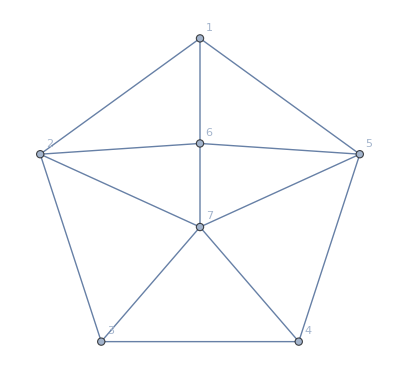

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->6,5<->6,6<->7,7<->3,7<->4,2<->7,5<->7},GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```